```mathematica
ZrC uncoupled anharmonic Einstein oscillators
```

anharmonic Einstein oscillators uncoupled ZrC

0.0263295

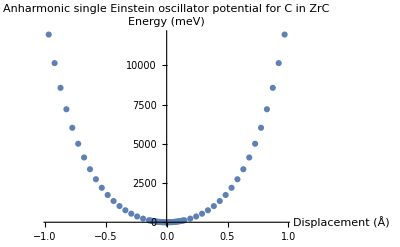

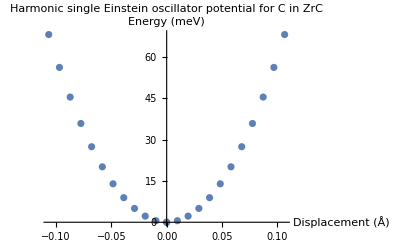

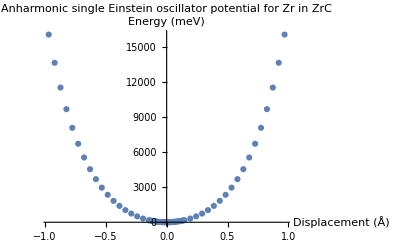

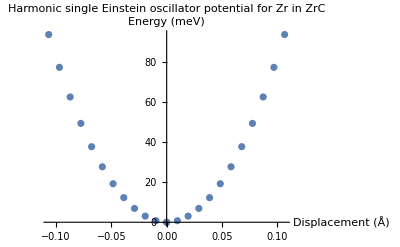

```mathematica
Method;
(*H.J.Korsch and M Glück,"Computing quantum eigenvalues made easy" Eur.J.Phys.23 (2002) 413-426.
ftp://ftp.physics.uwa.edu.au/pub/Computational/References/Korsch%20and%20Gluck.pdf
*)
ClearAll;
Read in Einstein oscillator potential ab initio data;
zrEinsteinmeV=26.329538754361874/1000
cEinsteinmeV=65.1879672429008/1000;
m={12.0107,91.224,1};
(*Data in*)SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Einstein_oscillator_4685Ang_ZrC"];
(*OLD input files :filesEinsteinPot={"C_300_1900_3200K_energy_displacment","C_300_1900_32e00K_energy_displacement_harmonic"};*)
filesEinsteinPot={"C_3200K_energy_displacement","C_3200K_energy_displacement_harmonic","Zr_3200K_energy_displacement","Zr_3200K_energy_displacement_harmonic"};
CarbonPotentialEinstein=ReadList[filesEinsteinPot[[1]],{Number, Number}];
CarbonPotentialEinsteinHarmonic=ReadList[filesEinsteinPot[[2]],{Number, Number}];
Show@ListPlot[CarbonPotentialEinstein,PlotLabel->"Anharmonic single Einstein oscillator potential for C in ZrC",AxesLabel->{"Displacement (Å)","Energy (meV)"}]
Show@ListPlot[CarbonPotentialEinsteinHarmonic,PlotLabel->"Harmonic single Einstein oscillator potential for C in ZrC",AxesLabel->{"Displacement (Å)","Energy (meV)"}]
ZirconPotentialEinstein=ReadList[filesEinsteinPot[[3]],{Number, Number}];
ZirconPotentialEinsteinHarmonic=ReadList[filesEinsteinPot[[4]],{Number, Number}];
Show@ListPlot[ZirconPotentialEinstein,PlotLabel->"Anharmonic single Einstein oscillator potential for Zr in ZrC",AxesLabel->{"Displacement (Å)","Energy (meV)"}]
Show@ListPlot[ZirconPotentialEinsteinHarmonic,PlotLabel->"Harmonic single Einstein oscillator potential for Zr in ZrC",AxesLabel->{"Displacement (Å)","Energy (meV)"}]
```

```mathematica
Polynomial fit;
```

```mathematica
(*Carbon*)
V[1,2,x_]:=Fit[CarbonPotentialEinsteinHarmonic,{x^2},x]
V[1,4,x_]:=Fit[CarbonPotentialEinstein,{x^2,x^4},x]
V[1,6,x_]:=Fit[CarbonPotentialEinstein,{x^2,x^4,x^6},x]
V[1,8,x_]:=Fit[CarbonPotentialEinstein,{x^2,x^4,x^6,x^8},x]
V[1,10,x_]:=Fit[CarbonPotentialEinstein,{x^2,x^4,x^6,x^8,x^10},x]
(*I want to 'normalise' to make the Hamiltonian as simple as possible - should I normalise 1) with respect to the harmonic fitted prefractor, 2) with respect to the first derivitive of the potential, 3) with respect to the species mass in AMU. If I want to let omega=1, then it can't be 3), it has to 1 or 2*)
Vnorm[1,2,x_]:=V[1,2,x]/V[1,2,x][[1]]
Vnorm[1,4,x_]:=Fit[CarbonPotentialEinstein,{x^2,x^4},x]/V[1,2,x][[1]]
Vnorm[1,6,x_]:=Fit[CarbonPotentialEinstein,{x^2,x^4,x^6},x]/V[1,2,x][[1]]
Vnorm[1,8,x_]:=Fit[CarbonPotentialEinstein,{x^2,x^4,x^6,x^8},x]/V[1,2,x][[1]]
Vnorm[1,10,x_]:=Fit[CarbonPotentialEinstein,{x^2,x^4,x^6,x^8,x^10},x]/V[1,2,x][[1]]

(*Zirconium*)
V[2,2,x_]:=Fit[ZirconPotentialEinsteinHarmonic,{x^2},x]
V[2,4,x_]:=Fit[ZirconPotentialEinstein,{x^2,x^4},x]
V[2,6,x_]:=Fit[ZirconPotentialEinstein,{x^2,x^4,x^6},x]
V[2,8,x_]:=Fit[ZirconPotentialEinstein,{x^2,x^4,x^6,x^8},x]
V[2,10,x_]:=Fit[ZirconPotentialEinstein,{x^2,x^4,x^6,x^8,x^10},x]
(*Normalised Zr potentials*)
Vnorm[2,2,x_]:=Fit[ZirconPotentialEinsteinHarmonic,{x^2},x]/V[2,2,x][[1]]
Vnorm[2,4,x_]:=Fit[ZirconPotentialEinstein,{x^2,x^4},x]/V[2,2,x][[1]]
Vnorm[2,6,x_]:=Fit[ZirconPotentialEinstein,{x^2,x^4,x^6},x]/V[2,2,x][[1]]
Vnorm[2,8,x_]:=Fit[ZirconPotentialEinstein,{x^2,x^4,x^6,x^8},x]/V[2,2,x][[1]]
Vnorm[2,10,x_]:=Fit[ZirconPotentialEinstein,{x^2,x^4,x^6,x^8,x^10},x]/V[2,2,x][[1]]
```

```mathematica
(*Let f(x)=Acarbon*x*x=1/2*m*omega*omega*x*x*)
"A in eV/Ang**2 is"
Acarbon=V[1,2,X][[1]]
"C_Omega_0 in eV/Ang**2/AMU is approximately"
Omega=Sqrt[2Acarbon/m[[1]]]
(*Let f(x)=Acarbon*x*x=1/2*m*omega*omega*x*x*)
"A in eV/Ang**2 is"
Azirconium=V[2,2,X][[1]]
"C_Omega_0 in eV/Ang**2/AMU is approximately"
Omega=Sqrt[2Azirconium/m[[2]]]
```

A in eV/Ang**2 is

5991.98

C_Omega_0 in eV/Ang**2/AMU is approximately

31.5875

A in eV/Ang**2 is

8248.72

C_Omega_0 in eV/Ang**2/AMU is approximately

13.4479

```mathematica
V[1,4,x]
V[1,6,x]
V[1,10,x]
```

5478.87 x^2+7678.83 x^4

5924.76 x^2+6036.07 x^4+1318.73 x^6

5945.7 x^2+5776.38 x^4+2262.07 x^6-1305.04 x^8+608.52 x^10

```mathematica
(*Note because the mass of Carbon is 12 and the harmonic potential prefactor for the Carbon potential just happens to be 6eV the form of the Hamiltonian reduces to the textbook harmonic oscillator form with eigenvalue series 0.5 1.5 2.5 etc;
However this coincidence does not occur for Zr - the quadractic prefactor of around 8 is not equal to the half mass 91;
(*for V[1,2,X] (Carbon harmonic potential), 1/2 m0 ω^2 = 5.991 eV/Ang^2. omega = sqrt(2*5.99*1/12 ) = sqrt(1) = 1 [AMU*eV^0.5/Ang] *)
V[1,2,x]/1000/5.99197548078282
V[1,4,x]*0.001/5.99197548078282//Simplify
(*for V[2,2,X] (Zirconium harmonic potential), 1/2 m0 ω^2 = 8.25 eV/Ang^2. omega = sqrt(2*8.25*1/90 ) = sqrt(0.18333) = 0.4282 [AMU*eV^0.5/Ang] *)
V[2,2,x]/1000/8.248724499239167 
V[2,4,x]/1000/8.248724499239167 //Simplify*)
```

```mathematica
Plot 2^nd  4^th  6^th  8^th order fits against against true data;
(*Note C mean square displacement in ZrC is of the order 0.05Å^2 in ZrC, or RMS displacment of ~0.25Å - look at displacements up to ~0.5Å*)
(*Note Zr mean square displacement in ZrC is of the order 0.05Å^2 in ZrC, or RMS displacment of ~0.25Å - look at displacements up to ~0.5Å*)
CarbonPotentialEinstein//MatrixForm;
CarbonPotentialEinsteinHarmonic//MatrixForm;
```

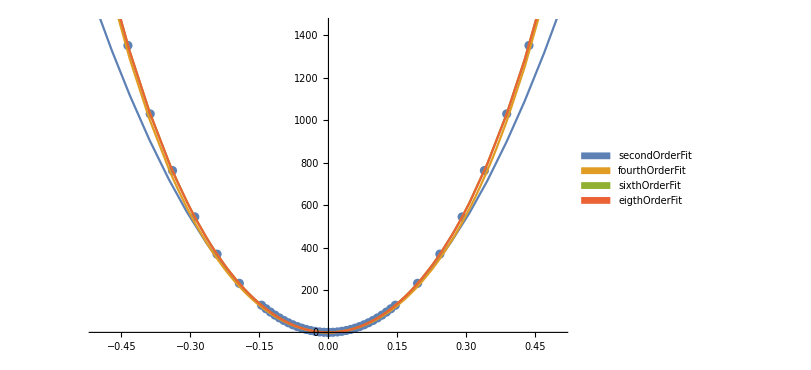

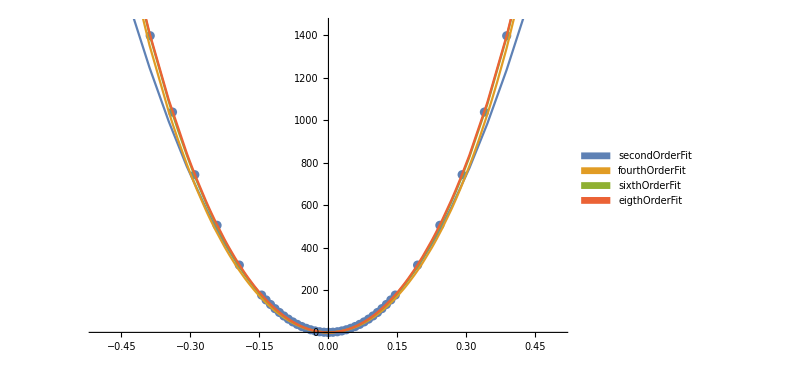

```mathematica
cdataPlot=ListPlot[CarbonPotentialEinstein,ImageSize->600, PlotRange->{{-0.5,0.5},{0,1450}}];
cFitsPlot=Plot[Evaluate@{V[1,2,x],V[1,4,x],V[1,6,x],V[1,8,x]},{x,-1,1},PlotLegends->SwatchLegend[nOrderFit],PlotLabel->"Polynomials fitted to anharmonic single Einstein oscillator potential for C in ZrC",AxesLabel->{"Displacement (Å)","Energy (meV)"}];
nOrderFit={secondOrderFit,fourthOrderFit,sixthOrderFit,eigthOrderFit,tenthOrderFit};
zdataPlot=ListPlot[ZirconPotentialEinstein,ImageSize->600, PlotRange->{{-0.5,0.5},{0,1450}}];
zFitsPlot=Plot[Evaluate@{V[2,2,x],V[2,4,x],V[2,6,x],V[2,8,x]},{x,-1,1},PlotLegends->SwatchLegend[nOrderFit],PlotLabel->"Polynomials fitted to anharmonic single Einstein oscillator potential for Zr in ZrC",AxesLabel->{"Displacement (Å)","Energy (meV)"}];
Show[{cdataPlot,cFitsPlot}]
Show[{zdataPlot,zFitsPlot}]
```

```mathematica
1/1000 V[1,8,x]//Simplify
```

5.91768 x^2+6.08441 x^4+1.22617 x^6+0.0528895 x^8

```mathematica
Normalised plots of 2^nd, 4^th, 6^th,8^th order fits
```

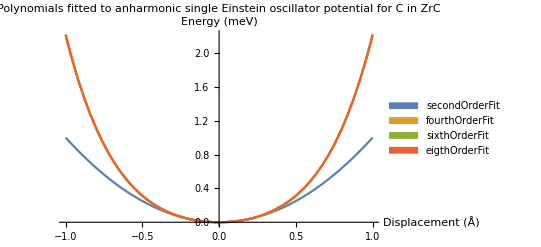

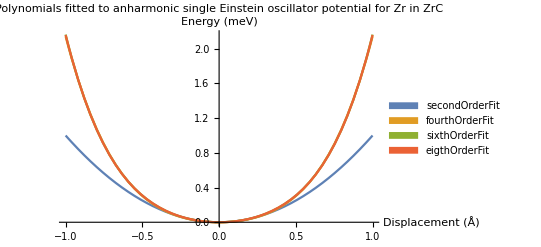

```mathematica
cFitsPlotnorm=Plot[Evaluate@{Vnorm[1,2,x],Vnorm[1,4,x],Vnorm[1,6,x],Vnorm[1,8,x]},{x,-1,1},PlotLegends->SwatchLegend[nOrderFit],PlotLabel->"Polynomials fitted to anharmonic single Einstein oscillator potential for C in ZrC",AxesLabel->{"Displacement (Å)","Energy (meV)"}]
zFitsPlotnorm=Plot[Evaluate@{Vnorm[2,2,x],Vnorm[2,4,x],Vnorm[2,6,x],Vnorm[2,8,x]},{x,-1,1},PlotLegends->SwatchLegend[nOrderFit],PlotLabel->"Polynomials fitted to anharmonic single Einstein oscillator potential for Zr in ZrC",AxesLabel->{"Displacement (Å)","Energy (meV)"}]
```

```mathematica
Units and conversion factors;
"H=T+V, T=-(ℏ^2/(2*m)*Laplacian";
"ℏ=m=ω=1";"ℏ=6.582119514(40)×10−16 eVs or 1.054571800(13)×10−34 Js";
(*massZr=91.224, massC=12.0107*)
"12.0107amu = 1.994423482e-26 Kg";
m={12.0107,91.224,1};
p=(ℏ^2/(m));
```

```mathematica
(*Code*)
"Position basis potential operator matrix";
xOp[dim_]:=SparseArray[{Band[{1,2}]->#,Band[{2,1}]->#},{#,#}&@dim]&[Table[Sqrt[i],{i,dim-1}]/Sqrt[2]]

"Laplacian operator expressed as a sparse tri-diagonal-ish matrix";
eKin[dim_]:=1/2 SparseArray[{Band[{1,1}]->Table[i-1/2,{i,dim}],Band[{1,3}]->#,Band[{3,1}]->#},{#,#}&@dim]&[Table[-Sqrt[i (i+1)/2],{i,dim-2}]/Sqrt[2]]
MatrixForm[xOp[8]];
MatrixForm[eKin[8]];

(*Hamiltonian matrix operators for 1-d Schrodinger equation - basis schown for 2-8*)
Table[{MatrixForm[xOp[i]],MatrixForm[eKin[i]]},{i,3,8}]//MatrixForm;
```

```mathematica
"spectrum[n,mass(1=C,2=Zr),tolerance][potential,var] solve the eigensystem for n eigenvalues and vectors. The number of basis states is determined to";
spectrum[n_,mass_,tolerance_: .0001][potential_,var_]/;PolynomialQ[potential,var]:=Module[{x,h,e,v,c=CoefficientList[potential,var],min=First@Check[Minimize[potential,var],Print["No absolute potential minimum found. Make sure the leading power has a positive coefficient!"];
Abort[],Minimize::natt]},
FixedPoint[{#[[1]]+1,Eigenvalues[h=(1/(m[[mass]]))*eKin[#[[1]]]+ 0.001*N[Sum[c[[i]] MatrixPower[xOp[#[[1]]],i-1],{i,2,Length[c]}]+(c[[1]]-min) IdentityMatrix[#[[1]]]],-n]}&,{n+1,2 Reverse@Range[n]-1},SameTest->(Max@Abs[#1[[2]]-#2[[2]]]<tolerance&)];
{e,v}=Reverse/@Eigensystem[h,-n];
{e+min,ψe/@v}]
spectrumnorm[n_,mass_,tolerance_: .0001][potential_,var_]/;PolynomialQ[potential,var]:=Module[{x,h,e,v,c=CoefficientList[potential,var],min=First@Check[Minimize[potential,var],Print["No absolute potential minimum found. Make sure the leading power has a positive coefficient!"];
Abort[],Minimize::natt]},
FixedPoint[{#[[1]]+1,Eigenvalues[h=1/2m [[mass]] eKin[#[[1]]]+ N[Sum[c[[i]] MatrixPower[xOp[#[[1]]],i-1],{i,2,Length[c]}]+(c[[1]]-min) IdentityMatrix[#[[1]]]],-n]}&,{n+1,2 Reverse@Range[n]-1},SameTest->(Max@Abs[#1[[2]]-#2[[2]]]<tolerance&)];
{e,v}=Reverse/@Eigensystem[h,-n];
{e+min,ψe/@v}]
```

```mathematica
Format[ψe[l_List]]:=ψe[Row[{"«",Length[l],"»"}]]
ψe[l_List][x_]:=1/(Pi^(1/4))Exp[-x^2/2] l.(1/Sqrt[2^# #!] HermiteH[#,x]&[Range[Length[l]]-1])

plotSpectrumnorm[data_,potential_,{var_,min_,max_}]:=Show[Apply[Plot[Evaluate[#1+(Last[#1]-First[#1])/(2+Length[#1])/2 Through[#2[var]]],{var,min,max},PlotLegends->SwatchLegend[data],Prolog->{Gray,Map[Line[{{min,#},{max,#}}]&,#1]},Frame->True]&,data],Plot[potential,{var,min,max}]]
plotSpectrum[data_,potential_,{var_,min_,max_}]:=Show[Apply[Plot[Evaluate[#1+(Last[#1]-First[#1])/(2+Length[#1])/2 Through[#2[var]]],{var,min,max},PlotLegends->SwatchLegend[data],Prolog->{Gray,Map[Line[{{min,#},{max,#}}]&,#1]},Frame->True]&,data],Plot[0.001*potential,{var,min,max}]]
```

5.99198 x^2

{{0.499443,1.49833,2.49721,3.4961,4.49499,5.49387,6.49276,7.49164,8.49052,9.48946},{ψe[«217»],ψe[«217»],ψe[«217»],ψe[«217»],ψe[«217»],ψe[«217»],ψe[«217»],ψe[«217»],ψe[«217»],ψe[«217»]}}

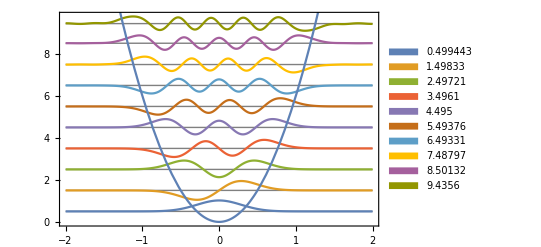

```mathematica
Carbon 2^nd order fit eigensystem;
1/1000 V[1,2,x]
c2=spectrum[10,1,0.0001][V[1,2,x],x]
With[{v= V[1,2,x],n=10},plotSpectrum[spectrum[n,1,0.1][v,x],v,{x,-2,2}]]
```

1. x^2

{{0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5},{ψe[«42»],ψe[«42»],ψe[«42»],ψe[«42»],ψe[«42»],ψe[«42»],ψe[«42»],ψe[«42»],ψe[«42»],ψe[«42»]}}

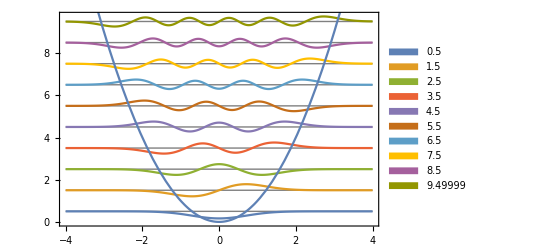

```mathematica
Carbon 2^nd order fit normalised eigensystem;
Vnorm[1,2,x]
c2n=spectrumnorm[10,3,0.000001][Vnorm[1,2,x],x]
With[{v= Vnorm[1,2,x],n=10},plotSpectrumnorm[spectrumnorm[n,3,0.00001][v,x],v,{x,-4,4}]]
```

8.24872 x^2

{{0.21263,0.637889,1.06315,1.48841,1.91367,2.33893,2.76419,3.18944,3.61471,4.03991},{ψe[«676»],ψe[«676»],ψe[«676»],ψe[«676»],ψe[«676»],ψe[«676»],ψe[«676»],ψe[«676»],ψe[«676»],ψe[«676»]}}

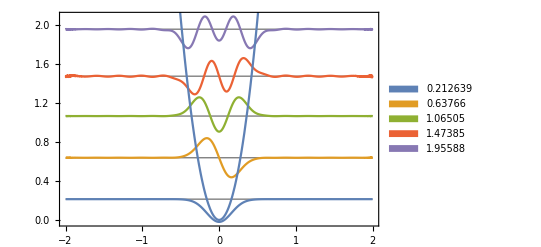

```mathematica
Zirconium 2^nd order fit eigensystem;
1/1000 V[2,2,x]
z2=spectrum[10,2,0.0001][V[2,2,x],x]
With[{v=V[2,2,x],n=5},plotSpectrum[spectrum[n,2,0.1][v,x],v,{x,-2,2}]]
```

1. x^2

{{0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5},{ψe[«42»],ψe[«42»],ψe[«42»],ψe[«42»],ψe[«42»],ψe[«42»],ψe[«42»],ψe[«42»],ψe[«42»],ψe[«42»]}}

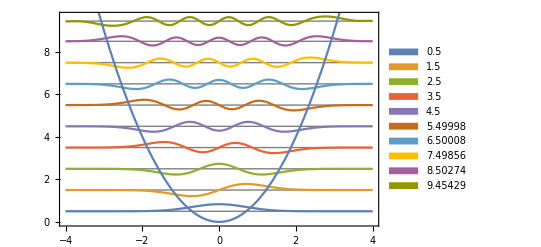

```mathematica
Normalised Zirconium 2^nd order fit eigensystem;
Vnorm[2,2,x]
z2n=spectrumnorm[10,3,0.000001][Vnorm[2,2,x],x]
With[{v=Vnorm[2,2,x],n=10},plotSpectrumnorm[spectrumnorm[n,3,0.1][v,x],v,{x,-4,4}]]
```

(5478.87 x^2+7678.83 x^4)/1000

{{0.514757,1.60603,2.807,4.09611,5.46048,6.89125,8.38188,9.92724,11.5232,13.1664},{ψe[«277»],ψe[«277»],ψe[«277»],ψe[«277»],ψe[«277»],ψe[«277»],ψe[«277»],ψe[«277»],ψe[«277»],ψe[«277»]}}

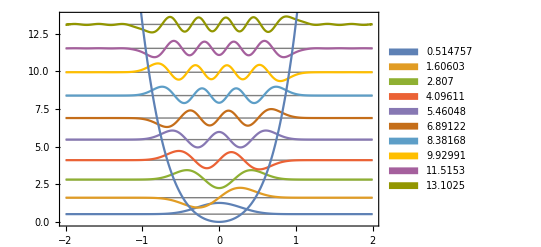

```mathematica
Carbon 4^th order fit eigensystem;
1/1000 V[1,4,x]
c4=spectrum[10,1,0.0001][V[1,4,x],x]
With[{v= V[1,4,x],n=10},plotSpectrum[spectrum[n,1,0.1][v,x],v,{x,-2,2}]]
```

0.00016689 (5478.87 x^2+7678.83 x^4)

{{0.630027,2.08245,3.84454,5.81601,7.95663,10.2414,12.6531,15.179,17.809,20.5352},{ψe[«109»],ψe[«109»],ψe[«109»],ψe[«109»],ψe[«109»],ψe[«109»],ψe[«109»],ψe[«109»],ψe[«109»],ψe[«109»]}}

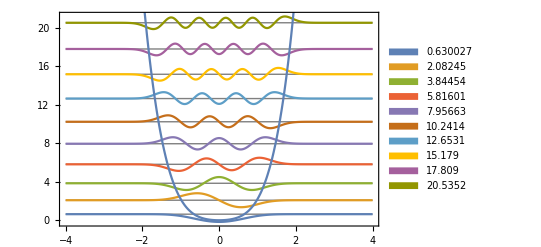

```mathematica
Normalised Carbon 4^th order fit normalised eigensystem;
Vnorm[1,4,x]
c4n=spectrumnorm[10,3,0.000001][Vnorm[1,4,x],x]
With[{v= Vnorm[1,4,x],n=10},plotSpectrumnorm[spectrumnorm[n,3,0.00001][v,x],v,{x,-4,4}]]
```

(7389.57 x^2+10278. x^4)/1000

{{0.206638,0.629881,1.07195,1.53088,2.00518,2.49365,2.99533,3.50938,4.03515,4.57194},{ψe[«657»],ψe[«657»],ψe[«657»],ψe[«657»],ψe[«657»],ψe[«657»],ψe[«657»],ψe[«657»],ψe[«657»],ψe[«657»]}}

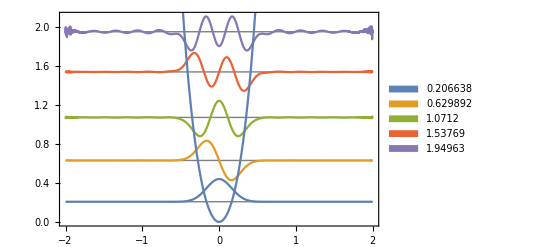

```mathematica
Zirconium 4^th order fit eigensystem;
1/1000 V[2,4,x]
z4=spectrum[10,2,0.0001][V[2,4,x],x]
With[{v= V[2,4,x],n=5},plotSpectrum[spectrum[n,2,0.1][v,x],v,{x,-2,2}]]
```

0.000121231 (7389.57 x^2+10278. x^4)

{{0.623884,2.06232,3.80766,5.76046,7.88087,10.1441,12.5331,15.0352,17.6405,20.3411},{ψe[«108»],ψe[«108»],ψe[«108»],ψe[«108»],ψe[«108»],ψe[«108»],ψe[«108»],ψe[«108»],ψe[«108»],ψe[«108»]}}

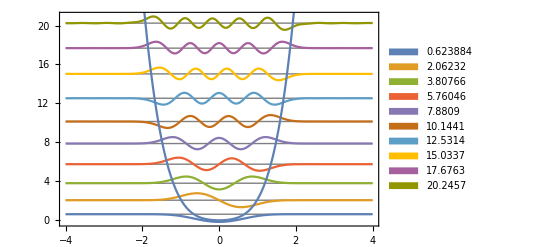

```mathematica
Normalised Zirconium 4^th order fit eigensystem;
Vnorm[2,4,x]
z4n=spectrumnorm[10,3,0.000001][Vnorm[2,4,x],x]
With[{v=Vnorm[2,4,x],n=10},plotSpectrumnorm[spectrumnorm[n,3,0.1][v,x],v,{x,-4,4}]]
```

(5924.76 x^2+6036.07 x^4+1318.73 x^6)/1000

{{0.52578,1.62903,2.82806,4.11023,5.46694,6.89178,8.37977,9.92689,11.5298,13.1857},{ψe[«272»],ψe[«272»],ψe[«272»],ψe[«272»],ψe[«272»],ψe[«272»],ψe[«272»],ψe[«272»],ψe[«272»],ψe[«272»]}}

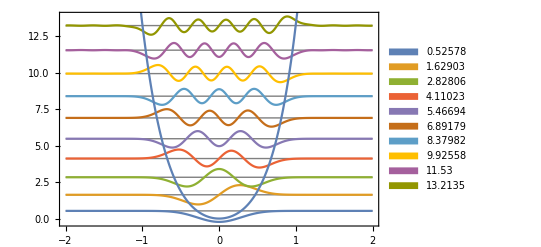

```mathematica
Carbon 6^th order fit eigensystem;
1/1000 V[1,6,x]
c6=spectrum[10,1,0.0001][V[1,6,x],x]
With[{v= V[1,6,x],n=10},plotSpectrum[spectrum[n,1,0.1][v,x],v,{x,-2,2}]]
```

0.00016689 (5924.76 x^2+6036.07 x^4+1318.73 x^6)

{{0.633819,2.09518,3.88871,5.93533,8.19659,10.6478,13.2714,16.0539,18.9844,22.0544},{ψe[«121»],ψe[«121»],ψe[«121»],ψe[«121»],ψe[«121»],ψe[«121»],ψe[«121»],ψe[«121»],ψe[«121»],ψe[«121»]}}

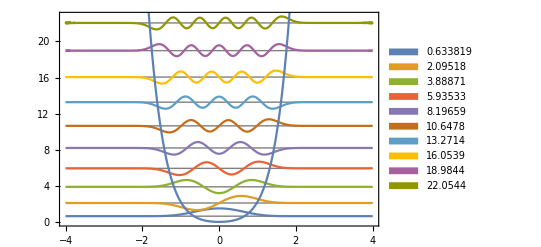

```mathematica
Normalised Carbon 6^th order fit normalised eigensystem;
Vnorm[1,6,x]
c6n=spectrumnorm[10,3,0.000001][Vnorm[1,6,x],x]
With[{v= Vnorm[1,6,x],n=10},plotSpectrumnorm[spectrumnorm[n,3,0.00001][v,x],v,{x,-4,4}]]
```

(8051. x^2+7841.1 x^4+1956.19 x^6)/1000

{{0.213964,0.649365,1.09926,1.56282,2.03934,2.52821,3.0289,3.54095,4.06393,4.59752},{ψe[«703»],ψe[«703»],ψe[«703»],ψe[«703»],ψe[«703»],ψe[«703»],ψe[«703»],ψe[«703»],ψe[«703»],ψe[«703»]}}

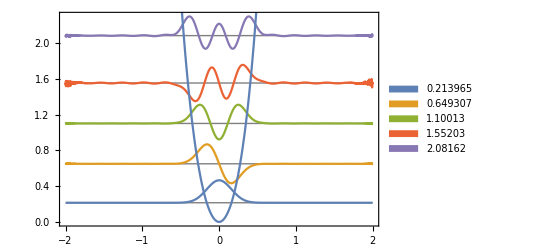

```mathematica
Ziroconium 6^th order fit eigensystem;
1/1000 V[2,6,x]
z6=spectrum[10,2,0.0001][V[2,6,x],x]
With[{v= V[2,6,x],n=5},plotSpectrum[spectrum[n,2,0.1][v,x],v,{x,-2,2}]]
```

0.000121231 (8051. x^2+7841.1 x^4+1956.19 x^6)

{{0.628046,2.07655,3.85701,5.89286,8.14585,10.5913,13.2115,15.9928,18.9246,21.9979},{ψe[«121»],ψe[«121»],ψe[«121»],ψe[«121»],ψe[«121»],ψe[«121»],ψe[«121»],ψe[«121»],ψe[«121»],ψe[«121»]}}

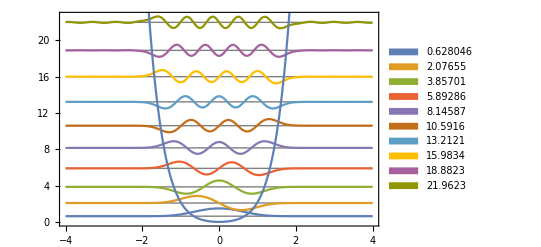

```mathematica
Normalised Zirconium 6^th order fit eigensystem;
Vnorm[2,6,x]
z6n=spectrumnorm[10,3,0.000001][Vnorm[2,6,x],x]
With[{v=Vnorm[2,6,x],n=10},plotSpectrumnorm[spectrumnorm[n,3,0.1][v,x],v,{x,-4,4}]]
```

(5917.68 x^2+6084.41 x^4+1226.17 x^6+52.8895 x^8)/1000

{{0.525655,1.62884,2.82798,4.11025,5.46698,6.89179,8.37974,9.92684,11.5298,13.1858},{ψe[«273»],ψe[«273»],ψe[«273»],ψe[«273»],ψe[«273»],ψe[«273»],ψe[«273»],ψe[«273»],ψe[«273»],ψe[«273»]}}

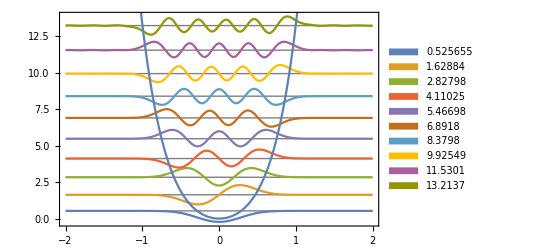

```mathematica
Carbon 8^th order fit eigensystem;
1/1000 V[1,8,x]
c8=spectrum[10,1,0.0001][V[1,8,x],x]
With[{v= V[1,8,x],n=10},plotSpectrum[spectrum[n,1,0.1][v,x],v,{x,-2,2}]]
```

0.00016689 (5917.68 x^2+6084.41 x^4+1226.17 x^6+52.8895 x^8)

{{0.633864,2.09563,3.89059,5.94073,8.20883,10.671,13.3103,16.1137,19.0708,22.1731},{ψe[«120»],ψe[«120»],ψe[«120»],ψe[«120»],ψe[«120»],ψe[«120»],ψe[«120»],ψe[«120»],ψe[«120»],ψe[«120»]}}

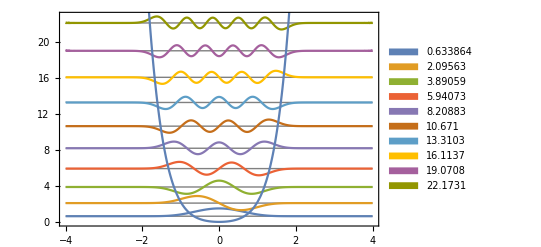

```mathematica
Normalised Carbon 8^th order fit normalised eigensystem;
Vnorm[1,8,x]
c8n=spectrumnorm[10,3,0.000001][Vnorm[1,8,x],x]
With[{v= Vnorm[1,8,x],n=10},plotSpectrumnorm[spectrumnorm[n,3,0.00001][v,x],v,{x,-4,4}]]
```

(8251.8 x^2+6469. x^4+4583.31 x^6-1501.17 x^8)/1000

{{0.215914,0.654157,1.10516,1.56873,2.04461,2.53249,3.03207,3.5429,4.06562,4.59213},{ψe[«592»],ψe[«592»],ψe[«592»],ψe[«592»],ψe[«592»],ψe[«592»],ψe[«592»],ψe[«592»],ψe[«592»],ψe[«592»]}}

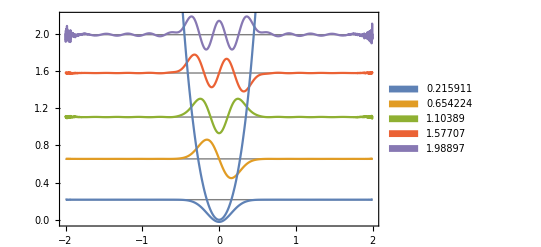

```mathematica
Zirconium 8^th order fit eigensystem;
1/1000 V[2,8,x]
z8=spectrum[10,2,0.01][V[2,8,x],x]
With[{v= V[2,8,x],n=5},plotSpectrum[spectrum[n,2,0.1][v,x],v,{x,-2,2}]]
```

```mathematica
Normalised Zirconium 8^th order fit eigensystem;
Vnorm[2,8,x]//Simplify
```

{{0.62693,2.06523,3.80758,5.73491,7.70652},{ψe[«38»],ψe[«38»],ψe[«38»],ψe[«38»],ψe[«38»]}}

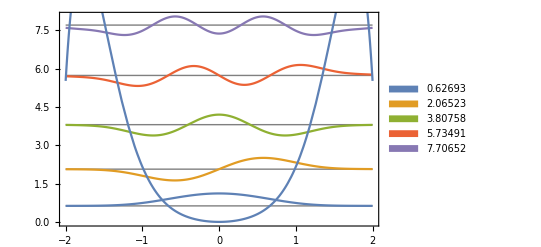

```mathematica
z8n=spectrumnorm[5,3,0.1][Vnorm[2,8,x]//Simplify,x]
With[{v=Vnorm[2,8,x]//Simplify,n=5},plotSpectrumnorm[spectrumnorm[n,3,0.1][v,x],v,{x,-2,2}]]
```

(5945.7 x^2+5776.38 x^4+2262.07 x^6-1305.04 x^8+608.52 x^10)/1000

{{0.52599,1.62918,2.82789,4.11014,5.46706,6.89205,8.38006,9.92721,11.5305,13.1875},{ψe[«300»],ψe[«300»],ψe[«300»],ψe[«300»],ψe[«300»],ψe[«300»],ψe[«300»],ψe[«300»],ψe[«300»],ψe[«300»]}}

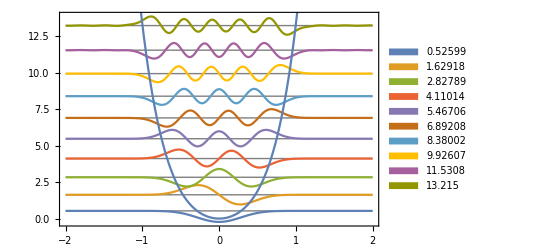

```mathematica
Carbon 10^th order fit eigensystem;
1/1000 V[1,10,x]
c10=spectrum[10,1,0.0001][V[1,10,x],x]
With[{v= V[1,10,x],n=10},plotSpectrum[spectrum[n,1,0.1][v,x],v,{x,-2,2}]]
```

0.00016689 (5945.7 x^2+5776.38 x^4+2262.07 x^6-1305.04 x^8+608.52 x^10)

{{0.634641,2.10151,3.91571,6.0162,8.38657,11.0215,13.9163,17.0654,20.4626,24.1017},{ψe[«186»],ψe[«186»],ψe[«186»],ψe[«186»],ψe[«186»],ψe[«186»],ψe[«186»],ψe[«186»],ψe[«186»],ψe[«186»]}}

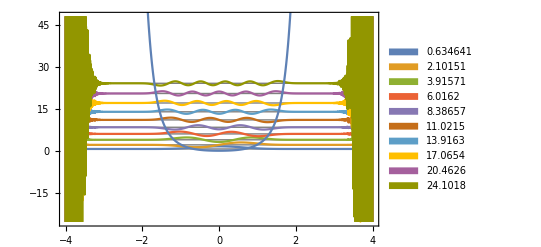

```mathematica
Normalised Carbon 10^th order fit normalised eigensystem;
Vnorm[1,10,x]
c10n=spectrumnorm[10,3,0.000001][Vnorm[1,10,x],x]
With[{v= Vnorm[1,10,x],n=10},plotSpectrumnorm[spectrumnorm[n,3,0.00001][v,x],v,{x,-4,4}]]
```

```mathematica
Zirconium 10^th order fit eigensystem;
1/1000 V[2,10,x]
z10=spectrum[10,2,0.1][V[2,10,x],x]
(*With[{v= V[2,10,x],n=5},plotSpectrum[spectrum[n,2,0.1][v,x],v,{x,-2,2}]]*)
```

(8139.37 x^2+7705.04 x^4+426.522 x^6+3947.84 x^8-2441.83 x^10)/1000

NMinimize::cvdiv: Failed to converge to a solution. The function may be unbounded.

$Aborted

NMinimize::cvdiv: Failed to converge to a solution. The function may be unbounded.

$Aborted

```mathematica
Normalised Zirconium 10^th order fit eigensystem;
Vnorm[2,10,x]
z10n=spectrumnorm[5,3,0.1][Vnorm[2,10,x],x]
With[{v=Vnorm[2,10,x],n=5},plotSpectrumnorm[spectrumnorm[n,3,0.1][v,x],v,{x,-2,2}]]
```

0.000121231 (8139.37 x^2+7705.04 x^4+426.522 x^6+3947.84 x^8-2441.83 x^10)

NMinimize::cvdiv: Failed to converge to a solution. The function may be unbounded.

$Aborted

$Aborted

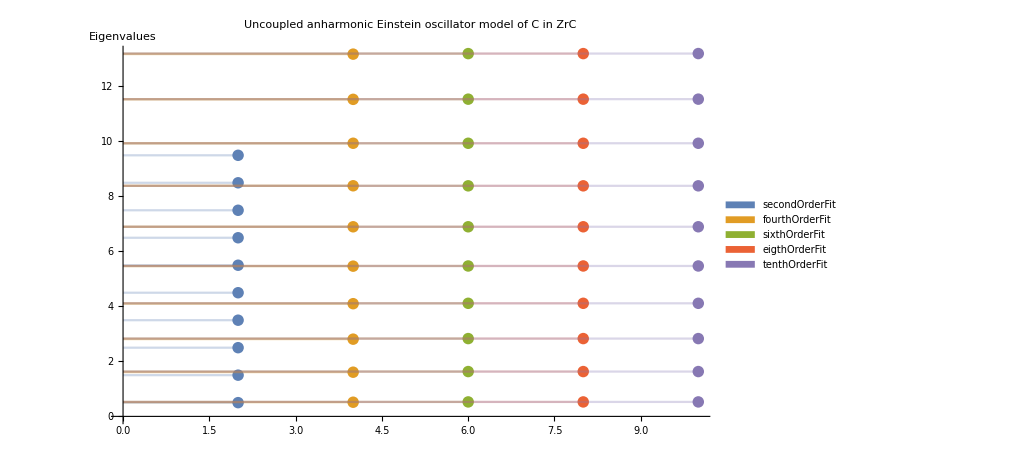

```mathematica
c={c2,c4,c6,c8,c10};
horizontalListPlotFill[listplot_,axisOrigin_: 0]:=listplot/.Point[a__]:>{Point[a],Opacity[0.3],Line[{{axisOrigin,#2},{#1,#2}}&@@@a]};
horizontalListPlotFill@ListPlot[Table[Table[{j*2i/i,c[[j]][[1]][[i]]},{i,1,10}],{j,1,5}],AxesOrigin->{0,0},PlotLegends->SwatchLegend[nOrderFit],PlotLabel->"Uncoupled anharmonic Einstein oscillator model of C in ZrC",AxesLabel->{"","Eigenvalues"},ImageSize->750]
```

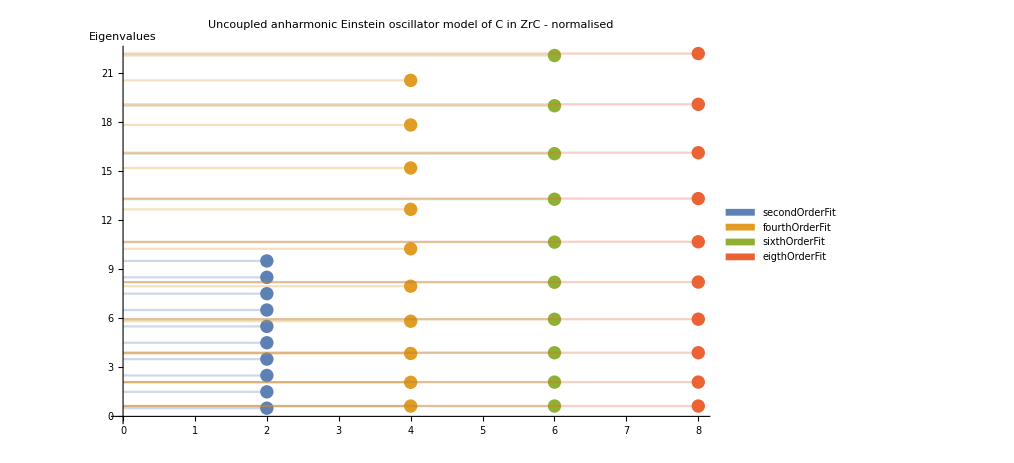

```mathematica
cn={c2n,c4n,c6n,c8n};
horizontalListPlotFill[listplot_,axisOrigin_: 0]:=listplot/.Point[a__]:>{Point[a],Opacity[0.3],Line[{{axisOrigin,#2},{#1,#2}}&@@@a]};
horizontalListPlotFill@ListPlot[Table[Table[{j*2i/i,cn[[j]][[1]][[i]]},{i,1,10}],{j,1,4}],AxesOrigin->{0,0},PlotLegends->SwatchLegend[nOrderFit],PlotLabel->"Uncoupled anharmonic Einstein oscillator model of C in ZrC - normalised",AxesLabel->{"","Eigenvalues"},ImageSize->750]
```

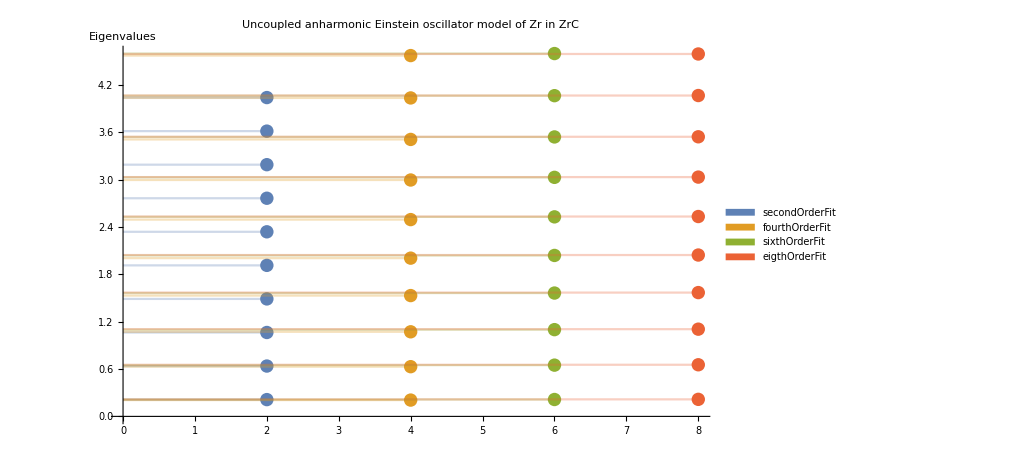

```mathematica
z={z2,z4,z6,z8};
horizontalListPlotFill[listplot_,axisOrigin_: 0]:=listplot/.Point[a__]:>{Point[a],Opacity[0.3],Line[{{axisOrigin,#2},{#1,#2}}&@@@a]};
horizontalListPlotFill@ListPlot[Table[Table[{j*2i/i,z[[j]][[1]][[i]]},{i,1,10}],{j,1,4}],AxesOrigin->{0,0},PlotLegends->SwatchLegend[nOrderFit],PlotLabel->"Uncoupled anharmonic Einstein oscillator model of Zr in ZrC",AxesLabel->{"","Eigenvalues"},ImageSize->750]
```

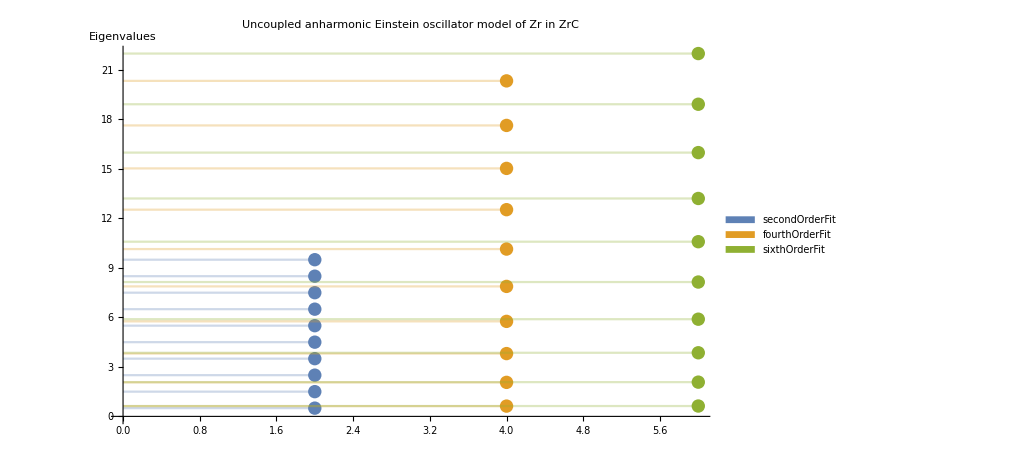

```mathematica
zn={z2n,z4n,z6n,z8n};
horizontalListPlotFill[listplot_,axisOrigin_: 0]:=listplot/.Point[a__]:>{Point[a],Opacity[0.3],Line[{{axisOrigin,#2},{#1,#2}}&@@@a]};
horizontalListPlotFill@ListPlot[Table[Table[{j*2i/i,zn[[j]][[1]][[i]]},{i,1,10}],{j,1,3}],AxesOrigin->{0,0},PlotLegends->SwatchLegend[nOrderFit],PlotLabel->"Uncoupled anharmonic Einstein oscillator model of Zr in ZrC",AxesLabel->{"","Eigenvalues"},ImageSize->750]
```

(0.499443 | 1.49833 | 2.49721 | 3.4961 | 4.49499 | 5.49387 | 6.49276 | 7.49164 | 8.49052 | 9.48946
0.514757 | 1.60603 | 2.807 | 4.09611 | 5.46048 | 6.89125 | 8.38188 | 9.92724 | 11.5232 | 13.1664
0.52578 | 1.62903 | 2.82806 | 4.11023 | 5.46694 | 6.89178 | 8.37977 | 9.92689 | 11.5298 | 13.1857
0.525655 | 1.62884 | 2.82798 | 4.11025 | 5.46698 | 6.89179 | 8.37974 | 9.92684 | 11.5298 | 13.1858
0.52599 | 1.62918 | 2.82789 | 4.11014 | 5.46706 | 6.89205 | 8.38006 | 9.92721 | 11.5305 | 13.1875)

(1.03066 | 1.07188 | 1.12405 | 1.17162 | 1.21479 | 1.25435 | 1.29096 | 1.32511 | 1.35718 | 1.38747
1.05273 | 1.08723 | 1.13249 | 1.17566 | 1.21623 | 1.25445 | 1.29063 | 1.32506 | 1.35796 | 1.38951
1.05248 | 1.0871 | 1.13245 | 1.17567 | 1.21624 | 1.25445 | 1.29063 | 1.32506 | 1.35796 | 1.38952
1.05315 | 1.08733 | 1.13242 | 1.17563 | 1.21626 | 1.2545 | 1.29068 | 1.3251 | 1.35804 | 1.3897)

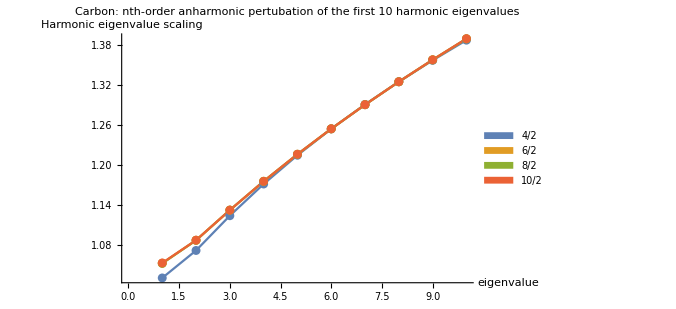

```mathematica
cEigenAll={c2[[1]],c4[[1]],c6[[1]],c8[[1]],c10[[1]]};
cEigenAll//MatrixForm
ratioNames={"4/2","6/2","8/2","10/2"};
cplotInfo={PlotLegends->SwatchLegend[ratioNames],PlotLabel->"Carbon: nth-order anharmonic pertubation\n of the first 10 harmonic eigenvalues",AxesLabel->{"eigenvalue","Harmonic eigenvalue\n scaling"},PlotStyle->Thick,ImageSize->500};
cRatios={cEigenAll[[2]]/cEigenAll[[1]],cEigenAll[[3]]/cEigenAll[[1]],cEigenAll[[4]]/cEigenAll[[1]],cEigenAll[[5]]/cEigenAll[[1]]};
cRatios//MatrixForm
Show[ListPlot[cRatios,Joined->True,cplotInfo],ListPlot[cRatios]]
```

(0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5
0.630027 | 2.08245 | 3.84454 | 5.81601 | 7.95663 | 10.2414 | 12.6531 | 15.179 | 17.809 | 20.5352
0.633819 | 2.09518 | 3.88871 | 5.93533 | 8.19659 | 10.6478 | 13.2714 | 16.0539 | 18.9844 | 22.0544
0.633864 | 2.09563 | 3.89059 | 5.94073 | 8.20883 | 10.671 | 13.3103 | 16.1137 | 19.0708 | 22.1731
0.634641 | 2.10151 | 3.91571 | 6.0162 | 8.38657 | 11.0215 | 13.9163 | 17.0654 | 20.4626 | 24.1017)

(1.26005 | 1.3883 | 1.53782 | 1.66172 | 1.76814 | 1.86208 | 1.94664 | 2.02387 | 2.09518 | 2.1616
1.26764 | 1.39678 | 1.55549 | 1.69581 | 1.82147 | 1.93597 | 2.04176 | 2.14051 | 2.23346 | 2.32151
1.26773 | 1.39709 | 1.55624 | 1.69735 | 1.82418 | 1.94019 | 2.04774 | 2.14849 | 2.24362 | 2.33401
1.26928 | 1.40101 | 1.56628 | 1.71891 | 1.86368 | 2.00391 | 2.14098 | 2.27539 | 2.40737 | 2.53703)

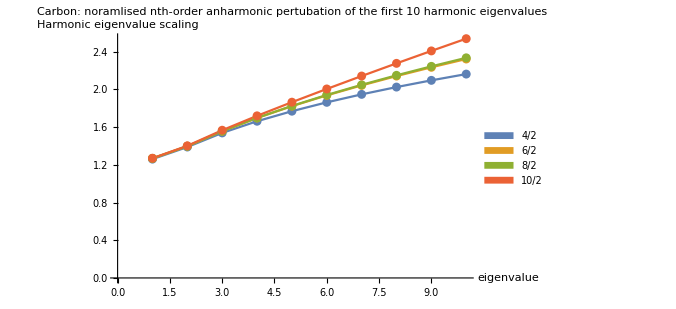

```mathematica
cEigenAlln={c2n[[1]],c4n[[1]],c6n[[1]],c8n[[1]],c10n[[1]]};
cEigenAlln//MatrixForm
ratioNames={"4/2","6/2","8/2","10/2"};
cplotInfo={PlotLegends->SwatchLegend[ratioNames],PlotLabel->"Carbon: noramlised nth-order anharmonic pertubation\n of the first 10 harmonic eigenvalues",AxesLabel->{"eigenvalue","Harmonic eigenvalue\n scaling"},PlotStyle->Thick,ImageSize->500};
cRatiosn={cEigenAlln[[2]]/cEigenAlln[[1]],cEigenAlln[[3]]/cEigenAlln[[1]],cEigenAlln[[4]]/cEigenAlln[[1]],cEigenAlln[[5]]/cEigenAlln[[1]]};
cRatiosn//MatrixForm
Show[ListPlot[cRatiosn,Joined->True,cplotInfo],ListPlot[cRatiosn]]
```

(0.21263 | 0.637889 | 1.06315 | 1.48841 | 1.91367 | 2.33893 | 2.76419 | 3.18944 | 3.61471 | 4.03991
0.206638 | 0.629881 | 1.07195 | 1.53088 | 2.00518 | 2.49365 | 2.99533 | 3.50938 | 4.03515 | 4.57194
0.213964 | 0.649365 | 1.09926 | 1.56282 | 2.03934 | 2.52821 | 3.0289 | 3.54095 | 4.06393 | 4.59752
0.215914 | 0.654157 | 1.10516 | 1.56873 | 2.04461 | 2.53249 | 3.03207 | 3.5429 | 4.06562 | 4.59213)

(0.971819 | 0.987446 | 1.00827 | 1.02853 | 1.04782 | 1.06615 | 1.08362 | 1.10031 | 1.11631 | 1.13169
1.00627 | 1.01799 | 1.03397 | 1.05 | 1.06567 | 1.08093 | 1.09577 | 1.11021 | 1.12428 | 1.13802
1.01544 | 1.0255 | 1.03952 | 1.05397 | 1.06842 | 1.08276 | 1.09691 | 1.11082 | 1.12474 | 1.13669)

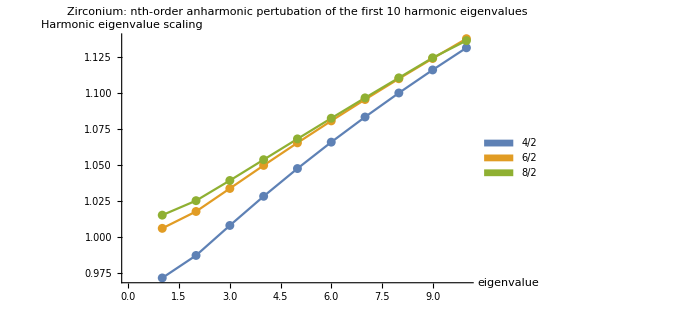

```mathematica
zEigenAll={z2[[1]],z4[[1]],z6[[1]],z8[[1]]};
zEigenAll//MatrixForm
ratioNames={"4/2","6/2","8/2"};
zplotInfo={PlotLegends->SwatchLegend[ratioNames],PlotLabel->"Zirconium: nth-order anharmonic pertubation\n of the first 10 harmonic eigenvalues",AxesLabel->{"eigenvalue","Harmonic eigenvalue\n scaling"},PlotStyle->Thick,ImageSize->500};
zRatios={zEigenAll[[2]]/zEigenAll[[1]],zEigenAll[[3]]/zEigenAll[[1]],zEigenAll[[4]]/zEigenAll[[1]]};
zRatios//MatrixForm
Show[ListPlot[zRatios,Joined->True,zplotInfo],ListPlot[zRatios]]
```

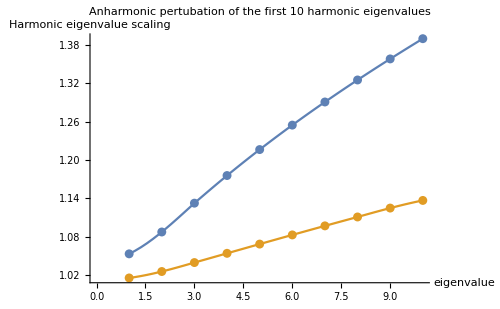

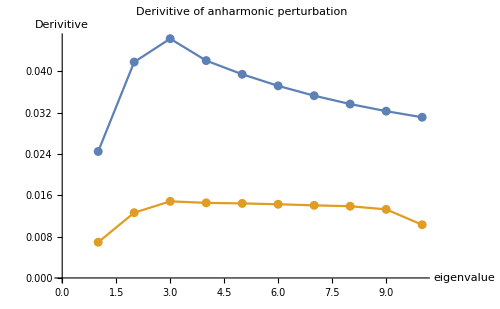

```mathematica
listPlot=ListPlot[{cRatios[[4]],zRatios[[3]]},anharmonicInfo];
c4Inter=Interpolation[cRatios[[4]]];
z3Inter=Interpolation[zRatios[[3]]];

anharmonicInfo={PlotLegends->SwatchLegend["Zirconium","Carbon"],PlotLabel->"Anharmonic pertubation of the first 10 harmonic eigenvalues",AxesLabel->{"eigenvalue","Harmonic eigenvalue\n scaling"},PlotStyle->Thick,ImageSize->500};
anharmonicDerivativeInfo={PlotLegends->SwatchLegend["Zirconium","Carbon"],PlotLabel->"Derivitive of anharmonic perturbation",AxesLabel->{"eigenvalue","Derivitive"},PlotStyle->Thick,ImageSize->500};

interPlot=Plot[{c4Inter[x],z3Inter[x]},{x,1,10}];
derivativePlot={ListPlot[{c4Inter',z3Inter'},anharmonicDerivativeInfo],ListPlot[{c4Inter',z3Inter'},Joined->True]};

Show[listPlot,interPlot]
Show[derivativePlot]
```

Part::partd: Part specification zRatiosn⟦3⟧ is longer than depth of object.

Interpolation::innd: First argument in zRatiosn⟦3⟧ does not contain a list of data and coordinates.

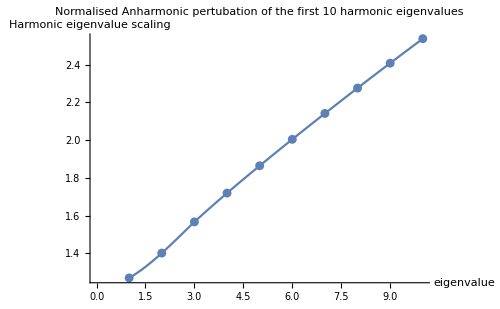

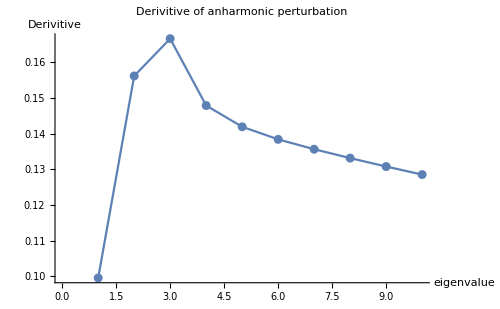

```mathematica
listPlotn=ListPlot[{cRatiosn[[4]],zRatiosn[[3]]},anharmonicInfon];
c4Intern=Interpolation[cRatiosn[[4]]];
z3Intern=Interpolation[zRatiosn[[3]]];

anharmonicInfon={PlotLegends->SwatchLegend["Zirconium","Carbon"],PlotLabel->"Anharmonic pertubation of the first 10 harmonic eigenvalues",AxesLabel->{"eigenvalue","Harmonic eigenvalue\n scaling"},PlotStyle->Thick,ImageSize->500};
anharmonicDerivativeInfon={PlotLegends->SwatchLegend["Zirconium","Carbon"],PlotLabel->"Derivitive of anharmonic perturbation",AxesLabel->{"eigenvalue","Derivitive"},PlotStyle->Thick,ImageSize->500};

interPlotn=Plot[{c4Intern[x],z3Intern[x]},{x,1,10}];
derivativePlotn={ListPlot[{c4Intern',z3Intern'},anharmonicDerivativeInfon],ListPlot[{c4Intern',z3Intern'},Joined->True]};

Show[listPlotn,interPlotn]
Show[derivativePlotn]
```

Part::partd: Part specification zRatiosn⟦3⟧ is longer than depth of object.

Interpolation::innd: First argument in zRatiosn⟦3⟧ does not contain a list of data and coordinates.

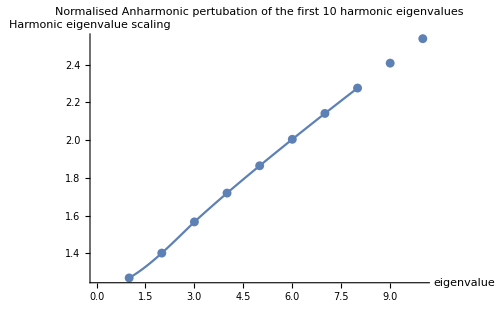

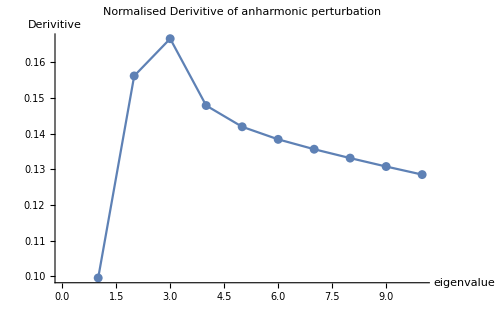

```mathematica
listPlotn=ListPlot[{cRatiosn[[4]],zRatiosn[[3]]},anharmonicInfon];
c4Intern=Interpolation[cRatiosn[[4]]];
z3Intern=Interpolation[zRatiosn[[3]]];

anharmonicInfon={PlotLegends->SwatchLegend["Zirconium","Carbon"],PlotLabel->"Normalised Anharmonic pertubation of the first 10 harmonic eigenvalues",AxesLabel->{"eigenvalue","Harmonic eigenvalue\n scaling"},PlotStyle->Thick,ImageSize->500};
anharmonicDerivativeInfon={PlotLegends->SwatchLegend["Zirconium","Carbon"],PlotLabel->"Normalised Derivitive of anharmonic perturbation",AxesLabel->{"eigenvalue","Derivitive"},PlotStyle->Thick,ImageSize->500};

interPlotn=Plot[{c4Intern[x],z3Intern[x]},{x,1,8}];
derivativePlotn={ListPlot[{c4Intern',z3Intern'},anharmonicDerivativeInfon],ListPlot[{c4Intern',z3Intern'},Joined->True]};

Show[listPlotn,interPlotn]
Show[derivativePlotn]
```